```mathematica
l[y_]:=(ct r0-cr r1+cr y-ct y)/(r0-r1)
```

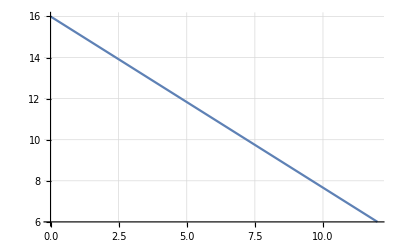

```mathematica
Plot[l[y]/.{cr-> 11, ct-> 6, r0-> 6, r1-> 12},{y,0,12},GridLines->Automatic]
```

```mathematica
diyy = Integrate[x^2 (rho t ),{x,y Tan[γ], y Tan[γ]+l[y]}]//Simplify
```

1/3 rho t (-y^3 Tan[γ]^3+((ct r0-cr r1+cr y-ct y)/(r0-r1)+y Tan[γ])^3)

```mathematica
IyyLE=Integrate[diyy, {y,r0, r1}]//Simplify
```

1/12 rho t (r0^4 Tan[γ]^3-r1^4 Tan[γ]^3+((r0-r1) (-(cr+r0 Tan[γ])^4+(ct+r1 Tan[γ])^4))/(cr-ct+(r0-r1) Tan[γ]))

```mathematica
m=Integrate[rho t l[y],{y,r0, r1}]/.r1-> r0+s//Simplify
```

1/2 (cr+ct) rho s t

```mathematica
cmx = (1/m)*Integrate[(y Tan[γ]+l[y]/2)(rho t l[y]),{y,r0, r1}]/.r1-> r0+s//Simplify
```

```mathematica
(cr^2+cr ct+ct^2+(3 cr r0+3 ct r0+cr s+2 ct s) Tan[γ])/(3 (cr+ct))//FullSimplify
```

(cr^2+cr ct+ct^2+(3 (cr+ct) r0+(cr+2 ct) s) Tan[γ])/(3 (cr+ct))

```mathematica
IyyLE2=IyyLE/.r1-> r0+s//FullSimplify//Apart//Cancel//Simplify
```

1/12 rho s t (cr^3+cr^2 ct+cr ct^2+ct^3+(2 cr ct (2 r0+s)+cr^2 (4 r0+s)+ct^2 (4 r0+3 s)) Tan[γ]+(cr (6 r0^2+4 r0 s+s^2)+ct (6 r0^2+8 r0 s+3 s^2)) Tan[γ]^2)

```mathematica
IyyLE2 - m cmx^2//FullSimplify
```

1/(36 (cr+ct))rho s t (cr^4+2 cr^3 ct+2 cr ct^3+ct^4-(cr^2+4 cr ct+ct^2) s Tan[γ] (cr-ct-s Tan[γ]))

```mathematica
(IyyLE2 - m cmx^2)/m//FullSimplify
```

1/(18 (cr+ct)^2)(cr^4+2 cr^3 ct+2 cr ct^3+ct^4-(cr^2+4 cr ct+ct^2) s Tan[γ] (cr-ct-s Tan[γ]))